# Soma Neuron Models

## Quadratic Neuron

### Bifurcation Model and Quadratic Firing Rate Model

τ_m v_m^•= -v_m+v_m^2/2+ v_in
v_in=ρ_qua I_c^2/I_l^2
τ_m= ρ_tau/I_l
τ_ref=ρ_ref/I_ref
f[v_in]=1/(τ_m·h[V_in] + t_ref)

```mathematica
VmdotTheory[Vm_,iin_,τ_]:=(1/2 Vm^2-Vm + iin)/τ
VmdotStackedBias[Vm_,Ic_,Il_,τ_,pqua_] :=(1/2 Vm^2-Vm + VinStackedBias[Ic,Il,pqua])/τ
VmdotDualBias[Vm_,Iin_,Il_,τ_,pqua_] :=(1/2 Vm^2-Vm + VinDualBias[Iin,Il,pqua])/τ
VinStackedBias[Ic_,Il_,pqua_]:=pqua(Ic/Il)^2
VinDualBias[Iin_,Il_,pqua_]:=pqua(Iin/Il)
τ[Il_,ptau_]:=ptau/Il
tref[Iref_,pref_]:=pref/Iref
f[Vin_,τ_,tref_]:=1/(τ h[Vin]+tref)
h[Vin_]:=(π+2ArcCot[√(-1+2Vin)])/(√(-1+2Vin))
labelSize=12;
titleLabelSize=14;
ImgSize=300;
TabView[{
"Theoretical (Dimensionless)"->DynamicModule[{iin=.51,tau=.015,tauref=0.001,, vmMax=5, vdotMin = 0,vdotMax=20, vinMax=2,fMax = 40, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["i_in",labelSize],Slider[Dynamic[iin],{0.01,2}],InputField[Dynamic[iin],FieldSize->5]},
{Style["τ_m",labelSize],Slider[Dynamic[tau],{0.001,.050,0.001}],InputField[Dynamic[tau],FieldSize->5]},{Style["t_ref",labelSize],Slider[Dynamic[tauref],{0.001,0.02,0.001}],InputField[Dynamic[tauref],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[iin],Background->LightGray]},
{Style["τ_m",labelSize],Panel[Dynamic[tau],Background->LightGray]},
{Style["t_ref",labelSize],Panel[Dynamic[tauref],Background->LightGray]}},
Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{VmdotTheory[Vmem,iin,tau]},{Vmem,0,vmMax},PlotRange->{vdotMin,vdotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,vin≤0},{f[vin,tau,tauref],vin>0.5}}],
Piecewise[{{0,vin≤0},{f[vin,tau,0],vin>0.5}}],
f[iin,tau,tauref],
f[iin,tau,0]},
{vin,0,vinMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{iin,f[iin,tau,0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{iin,f[iin,tau,tauref]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[iin,tau, 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[iin,tau, tauref]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[iin,tau, 0]-f[iin,tau, tauref]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["v_m_max",labelSize],Slider[Dynamic[vmMax],{0.,20}],InputField[Dynamic[vmMax],FieldSize->5]},
{Style["(v̇)_min",labelSize],Slider[Dynamic[vdotMin],{-10,0}],InputField[Dynamic[vdotMin],FieldSize->5]},{Style["(v̇)_max",labelSize],Slider[Dynamic[vdotMax],{10,200}],InputField[Dynamic[vdotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["v_in_max",labelSize],Slider[Dynamic[vinMax],{0.5,100}],InputField[Dynamic[vinMax],FieldSize->5]},{Style["f(v_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
](*DynamicModule Theoretical Dimensionless =================================================*),
"Applied Dual Bias (I_in)"->DynamicModule[{Iin=.5,Il=.595,Iref=7.333,pqua=1.50316,ptau=0.00119,pref=0.022, vmMax=5, vdotMin = 0,vdotMax=20, vinMax=2,fMax = 175, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_in",labelSize],Slider[Dynamic[Iin],{0.01,5}],InputField[Dynamic[Iin],FieldSize->5]},{Style["I_l",labelSize],Slider[Dynamic[Il],{0.01,1,0.005}],InputField[Dynamic[Il],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,10}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[VinDualBias[Iin,Il,pqua]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τ[Il,ptau]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[tref[Iref,pref]],Background->LightGray]}},Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[VinDualBias[Iin,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]},
{Style["2/ρ_qua",labelSize],Panel[Dynamic[2/pqua],Background->LightGray]},
{Style["f(2/ρ_qua)",labelSize],Panel[Dynamic[f[VinDualBias[Iin,Il,2/pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{VmdotDualBias[Vmem,Iin,Il,τ[Il,ptau],pqua]},{Vmem,0,vmMax},PlotRange->{vdotMin,vdotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],tref[Iref,pref]],vin>0.5}}],
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],0],vin>0.5}}],
f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],tref[Iref,pref]],
f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],0]},
{vin,0,vinMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{VinDualBias[Iin,Il,pqua],f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinDualBias[Iin,Il,pqua],f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],tref[Iref,pref]],vin>0.5}}],
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],0],vin>0.5}}]*),
f[VinDualBias[Iin,Ilit,pqua],τ[Ilit,ptau],tref[Iref,pref]],
f[VinDualBias[Iin,Ilit,pqua],τ[Ilit,ptau],0]},
{Ilit,0,ilitMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Darker[Red],Blue},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{VinDualBias[Iin,Il,pqua],f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinDualBias[Iin,Il,pqua],f[VinDualBias[Iin,Il,pqua],τ[Il,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[VinDualBias[Iin,Il,pqua],τ[Il, ptau], 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[VinDualBias[Iin,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[VinDualBias[Iin,Il,pqua],τ[Il, ptau], 0]-f[VinDualBias[Iin,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["v_m_max",labelSize],Slider[Dynamic[vmMax],{0.,20}],InputField[Dynamic[vmMax],FieldSize->5]},
{Style["(v̇)_min",labelSize],Slider[Dynamic[vdotMin],{-10,0}],InputField[Dynamic[vdotMin],FieldSize->5]},{Style["(v̇)_max",labelSize],Slider[Dynamic[vdotMax],{10,200}],InputField[Dynamic[vdotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["v_in_max",labelSize],Slider[Dynamic[vinMax],{0.5,100}],InputField[Dynamic[vinMax],FieldSize->5]},{Style["f(v_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
](*DynamicModule Applied Dual Bias(Iin)==============================================================*),
"Applied Stacked Bias (I_c)"-> DynamicModule[{Ic=.5,Il=.595,Iref=7.333,pqua=1.50316,ptau=0.00119,pref=0.022, vmMax=5, vdotMin = 0,vdotMax=20, vinMax=2,fMax = 175, ilitMax=3},
Panel[
Grid[{
{Grid[
{{
Grid[{
{Style["I_c",labelSize],Slider[Dynamic[Ic],{0.01,5}],InputField[Dynamic[Ic],FieldSize->5]},{Style["I_l",labelSize],Slider[Dynamic[Il],{0.01,1,0.005}],InputField[Dynamic[Il],FieldSize->5]},{Style["I_ref",labelSize],Slider[Dynamic[Iref],{0.01,10}],InputField[Dynamic[Iref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["ρ_qua",labelSize],Slider[Dynamic[pqua],{0.5,6}],InputField[Dynamic[pqua],FieldSize->5]},{Style["ρ_tau",labelSize],Slider[Dynamic[ptau],{0.0001,0.005}],InputField[Dynamic[ptau],FieldSize->5]},{Style["ρ_ref",labelSize],Slider[Dynamic[pref],{0.,0.2}],InputField[Dynamic[pref],FieldSize->5]}},Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}],
Grid[{
{Style["v_in",labelSize],Panel[Dynamic[VinStackedBias[Ic,Il,pqua]],Background->LightGray]},{Style["τ_m",labelSize],Panel[Dynamic[τ[Il,ptau]],Background->LightGray]},{Style["t_ref",labelSize],Panel[Dynamic[tref[Iref,pref]],Background->LightGray]}},Alignment->{Left,Left},Spacings->{1,0}],
Grid[{
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]},
{Style["2/ρ_qua",labelSize],Panel[Dynamic[2/pqua],Background->LightGray]},
{Style["f(2/ρ_qua)",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,2/pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]}
}]
}},Spacings->{5,0}]},
{Grid[
{{
Panel[
Dynamic[
Plot[{VmdotStackedBias[Vmem,Ic,Il,τ[Il,ptau],pqua]},{Vmem,0,vmMax},PlotRange->{vdotMin,vdotMax},PlotLabel->Style["Bifurcation Model",titleLabelSize],AxesLabel->{Style["v_m",labelSize],Style["v̇",labelSize]},ImageSize->ImgSize]
]
],
Panel[
Dynamic[
Show[
Plot[{
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],tref[Iref,pref]],vin>0.5}}],
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],0],vin>0.5}}],
f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],tref[Iref,pref]],
f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],0]},
{vin,0,vinMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Blue, Darker[Red],{Dashed,Blue},{Dashed,Darker[Red]}},AxesLabel->{Style["v_in",labelSize],Style["f(v_in)",labelSize]},ImageSize->ImgSize],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]
]
]
],
Panel[
Dynamic[
Show[
Plot[{
(*Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],tref[Iref,pref]],vin>0.5}}],
Piecewise[{{0,vin≤0},{f[vin,τ[Il,ptau],0],vin>0.5}}]*),
f[VinStackedBias[Ic,Ilit,pqua],τ[Ilit,ptau],tref[Iref,pref]],
f[VinStackedBias[Ic,Ilit,pqua],τ[Ilit,ptau],0]},
{Ilit,0,ilitMax},AxesOrigin->{0,0},PlotRange->{0,fMax},PlotLabel->Style["Quadratic Neuron Firing Rate",titleLabelSize],PlotStyle-> {Darker[Red],Blue},AxesLabel->{Style["I_lk",labelSize],Style["f(I_lk)",labelSize]},ImageSize->ImgSize](*,
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],0]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}],
ListPlot[{{VinStackedBias[Ic,Il,pqua],f[VinStackedBias[Ic,Il,pqua],τ[Il,ptau],tref[Iref,pref]]}},PlotStyle->Darker[Green],PlotMarkers->{"●",Small}]*)
]
]
],
Grid[{
{Style["f_0",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τ[Il, ptau], 0]],Background->LightGray]},
{Style["f",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]},
{Style["Δf_ref",labelSize],Panel[Dynamic[f[VinStackedBias[Ic,Il,pqua],τ[Il, ptau], 0]-f[VinStackedBias[Ic,Il,pqua],τ[Il, ptau], tref[Iref, pref]]],Background->LightGray]}
}]
}},
Alignment->{Left,Left,Right}]},
{Grid[
{{
Grid[{
{Style["v_m_max",labelSize],Slider[Dynamic[vmMax],{0.,20}],InputField[Dynamic[vmMax],FieldSize->5]},
{Style["(v̇)_min",labelSize],Slider[Dynamic[vdotMin],{-10,0}],InputField[Dynamic[vdotMin],FieldSize->5]},{Style["(v̇)_max",labelSize],Slider[Dynamic[vdotMax],{10,200}],InputField[Dynamic[vdotMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,1},0.5}],
Grid[{
{Style["v_in_max",labelSize],Slider[Dynamic[vinMax],{0.5,100}],InputField[Dynamic[vinMax],FieldSize->5]},{Style["f(v_in)_max",labelSize],Slider[Dynamic[fMax],{10,1000}],InputField[Dynamic[fMax],FieldSize->5]}},
Alignment->{Left,Center,Left},Spacings->{{1,1,2},0.5}]
}},
Alignment->{Left,Left,Right},Spacings->{18,0}]}
},Alignment->{Center}]
](*Panel*)
](*DynamicModule Applied Stacked Bias(Ic)=================================================*)
},1](*TabView*)
```

123

### V_in vs H Plot

```mathematica
Series[h[vin],{vin,.5,0}]
```

(√2 π)/(√(vin-0.5))-2+O((vin-0.5)^1)

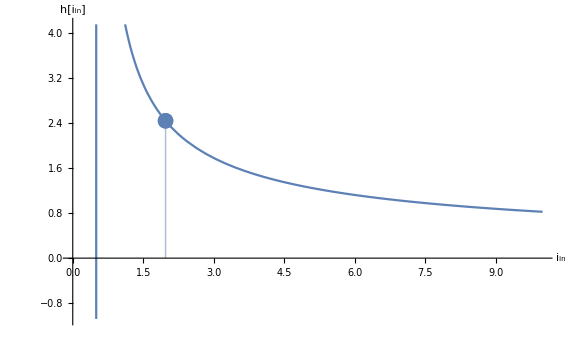

```mathematica
Show[
Plot[h[vin],{vin,0,10},ImageSize->Large,AxesLabel->{"i_in","h[i_in]"}],
ListPlot[{{1.97481,h[1.97481]}},Filling->Axis]
]
```

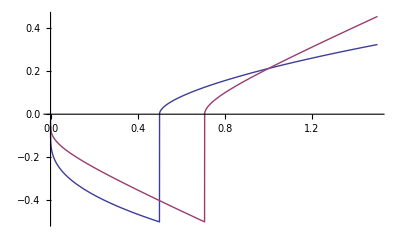

```mathematica
Plot[{h[vin]^-1,h[(vin)^2]^-1},{vin,0,1.5}]
```

Find out at what point the h[vin] function starts to explode (defined as when the slope is smaller than -1)

```mathematica
h[vin]
h'[vin]
dh[vin]=-(1/(vin (2 vin-1)))-(2 ArcCot[Sqrt[2 vin-1]]+π)/(2 vin-1)^(3/2)
```

(2 cot^-1(√(2 vin-1))+π)/(√(2 vin-1))

-1/(vin (2 vin-1))-(2 cot^-1(√(2 vin-1))+π)/(2 vin-1)^(3/2)

-1/(vin (2 vin-1))-(2 cot^-1(√(2 vin-1))+π)/(2 vin-1)^(3/2)

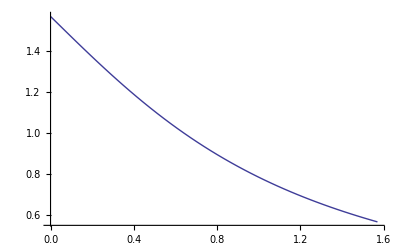

```mathematica
Plot[ArcCot[b],{b,0,π/2}]
```

```mathematica
FindRoot[dh[vin]==-1,{vin,1.5}]
```

{vin→1.97481}

```mathematica
h[{1.7,1.6, 0.6}]/0.03
```

{92.2631,97.2644,405.631}

```mathematica
Limit[h'[vin],vin->∞]
```

0

```mathematica
Limit[1/h[vin],vin->∞]
```

∞

```mathematica
Limit[1/dh[vin],vin->0.5]
```

0.

```mathematica
D[h[vin]^-2, vin]/.vin->{0.5,0.51,0.52}
```

{0.0506606,0.0580795,0.0614491}

Plot the slope of 1/h[i_in]for varying powers of h[i_in]in order to find when the plot is most linear

### Solve for Voltage Membrane

```mathematica
solution=DSolve[{Vm'[t]τ==1/2(Vm[t])^2-Vm[t]+VinStackedBias[Ic,Il,pqua], Vm[0]==1},Vm[t],t]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vm(t)→(√(2 Ic^2 pqua-Il^2) tan((t √(2 Ic^2 pqua-Il^2))/(2 Il τ))+Il)/Il}}

```mathematica
SetOptions[Plot, PlotPoints->400];
Manipulate[
solution=DSolve[{Vm'[t]τ==1/2(Vm[t])^2-Vm[t]+VinStackedBias[Ic,Il,pqua], Vm[0]==1},Vm[t],t][[1]];
Plot[Vm[t]/.solution,{t,0,10}],{{τ,.01},0,1,.05,Appearance->"Labeled"},{{Ic,.1},0.01,.3,.01,Appearance->"Labeled"},{{Il,.1},0.01,.2,.005,Appearance->"Labeled"},{{pqua,.51},0.5,6,.25,Appearance->"Labeled"},TrackedSymbols:>{τ,Ic,Il,pqua}]
```